## The Dihedral Group D_3

### Helper Functions

In order to display our vector graphics appropriately and to perform operations on these graphics, we need to work in a homogenous coordinate system. We will store our triangles as a 3x3 matrix, where the first two rows denote the points of the triangle and the third row is all ones. Thus, we will need a helper function in order to extract the points of the triangle we are actually interested in.

```mathematica
help[T_]:={T[[1;;2,1]],T[[1;;2,2]],T[[1;;2,3]]};
```

### Identity Triangle

The code below identifies our identity triangle, in homogenous coordinate systems, and then displays it using the Graphics and Triangle functions. In addition, we add labeling of our points for clarity.

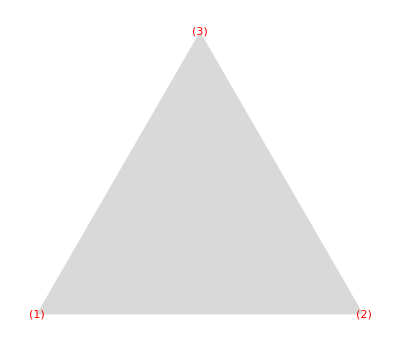

```mathematica
T={{0,2,1},{0,0,N[Sqrt[3]]},{1,1,1}};
Graphics[{{LightGray,Triangle[help[T]]},{help[T] /. {x_,y_} :> Text[Style[Position[help[T],{x,y}],Red],{x,y}]}}]
```

### Rotations

In order to rotate our triangle, we must first translate the triangle so that its midpoint is at the origin. Then, we apply a rotation matrix to our triangle and translate back. This is all done in homogenous coordinates. The code below defines the trans (translation), mid (midpoint), and rot (rotation) functions.

```mathematica
trans[T_,r_,s_]:={{1,0,r},{0,1,s},{0,0,1}}.T;
mid[T_]:=RegionCentroid[Triangle[help[T]]];
rot[T_,rad_]:=
Module[{r,s,Q},
{r,s}=mid[T];
Q={{Cos[rad],-Sin[rad],0},{Sin[rad],Cos[rad],0},{0,0,1}};
trans[Q.trans[T,-r,-s],r,s]];
```

Next, we show that what this rotation does to our triangle T using the Manipulate and Graphics function.

```mathematica
Manipulate[Graphics[{{LightGray,Triangle[help[rot[T,deg*Pi/180]]]},{help[rot[T,deg*Pi/180]] /. {x_,y_} :> Text[Style[Position[help[rot[T,deg*Pi/180]],{x,y}],Red],{x,y}]}}],{deg,0,360,10}]
```

### Reflection

The function below performs a reflection of our object through the line L that makes an angle deg with the origin. Just as with the rotation, we must first translate, then reflect, and then translate back

```mathematica
ref[T_,rad_]:=
Module[{r,s,Q},
{r,s}=mid[T];
Q={{Cos[2*rad],Sin[2*rad],0},{Sin[2*rad],-Cos[2*rad],0},{0,0,1}};
trans[Q.trans[T,-r,-s],r,s]];
```

Next, we show that what this reflection does to our triangle T using the Manipulate and Graphics function.

```mathematica
Manipulate[Graphics[{{LightGray,Triangle[help[ref[T,deg*Pi/180]]]},{help[ref[T,deg*Pi/180]] /. {x_,y_} :> Text[Style[Position[help[ref[T,deg*Pi/180]],{x,y}],Red],{x,y}]}}],{deg,0,360,10}]
```